# Integration

### Calculus II

In calculus you learned that
	∫_a^b f(x)dx=∫_t_0^t_1 f(x(t))x'(t)dt
where x was a smooth function satisfying x(t_0)=a and x(t_1)=b.  If t_0=0 and t_1=1 then the RHS integral could be computed as  
	∫_0^1 f(x(t))x'(t)dt=lim_(n->∞) ∑_(k=1)^n f(x(k Δt))x'(k Δt)Δt
with Δt=1/n. The RHS is one possible Riemann sum.  A Left/Right hand sum.

### Complex Analysis: FTC Entire Functions

The integral of f(z) along the contour c(t) in the complex plane from t_0 to t_1 is 
	∫_c f(z)dz=∫_t_0^t_1 f(z(t))z'(t)dt
where the contour c is defined by a function z(t) for t_0≤t≤t_1. If t_0=0 and t_1=1 then the RHS integral could be computed with the Riemann sum  
	∫_0^1 f(z(t))z'(t)dt=lim_(n->∞) ∑_(k=1)^n f(z(k Δt))z'(k Δt)Δt
with Δt=1/n. Amazingly the integral often only depends on the end points z(0) and z(1)!

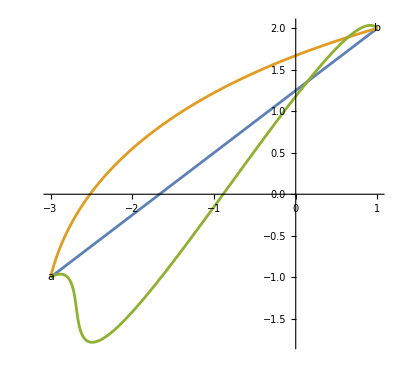

```mathematica
a=-3 - I;b=1+2I;
z1[t_]:=a(1-t) +b t
z2[t_]:= a(1-t) + b t + t(t-1)(3-I)
z3[t_]:= a(1-t) + b t + Sin[4t]Sin[3(t-1)](1+2I)
ParametricPlot[{
ReIm[z1[t]],
ReIm[z2[t]],
ReIm[z3[t]]
},{t,0, 1},
Epilog->{Text["a",ReIm[a]],Text["b",ReIm[b]]}]
```

```mathematica
a=-3 - I;b=1+2I;
z1[t_]:=a(1-t) +b t
z2[t_]:= a(1-t) + b t + t(t-1)(3-I)
z3[t_]:= a(1-t) + b t + Sin[4t]Sin[3(t-1)](1+2I)
f[z_]:= z Sin[z];
n=100;
Δt=1.0/n;
{Sum[f[z1[k Δt]]z1'[k Δt]Δt,{k,1,n}],
Sum[f[z2[k Δt]]z2'[k Δt]Δt,{k,1,n}],
Sum[f[z3[k Δt]]z3'[k Δt]Δt,{k,1,n}]}
```

{-0.560312+2.00191 ⅈ,-0.51538+2.07496 ⅈ,-0.336209+1.92254 ⅈ}

The analog of the calculus II fundamental theorem
	∫_a^b f(z)dz=F(b)-F(a)
works for entire functions in ℂ.  If f(z)=z sin(z) then F(z)=sin(z)-z cos(z)+const

```mathematica
F[z_]=Sin[z]-z Cos[z];
F[b]-F[a]
```

-0.33591+1.80778 ⅈ

For an entire function
	∮_c f(z)dz=0
for any closed contour c.

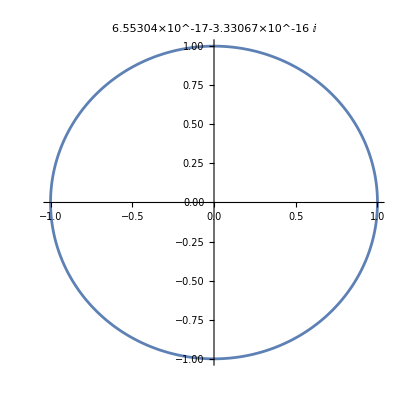

```mathematica
f[z_]:= Cos[Sin[z^2+Cos[z]]]
z[t_]:= E^(I 2 π t)
n=12; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

Lets try a more interesting contour

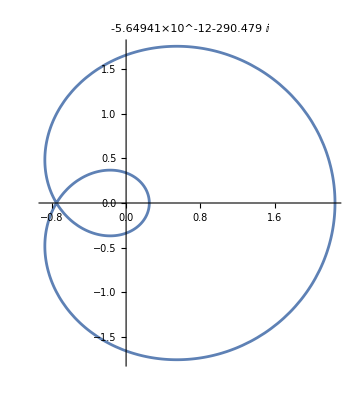

```mathematica
f[z_]:= Cos[Sin[z^2+Cos[z]]]
z[t_]:=( 0.5 +E^(I 2 π t))^2
n=12; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

### Complex Analysis: Functions with Poles

Here is an interesting contour and a simple function with a pole

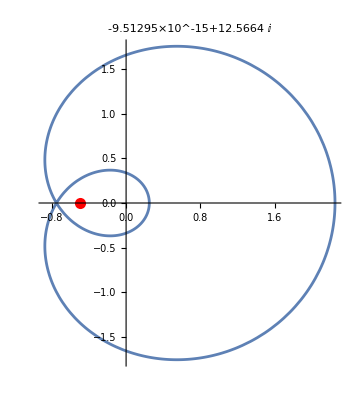

```mathematica
p=-0.5;f[z_]:= 1/(z-p)+z Cos[z^2];z[t_]:=( 0.5 +E^(I 2 π t))^2
n=1000; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
Epilog->{Red,PointSize[0.02], Point[ReIm[p]]},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

For a function 
	f(z)=r/(z-p)+g(z)
with g entire and any closed simple contour c traversed counterclockwise
	∮_c f(z)dz=Piecewise[{{0, if p is outside c}, {2π ⅈ r, if p is inside c}}]
The residue r satisfies
	r=lim_(z->p) (z-p)f[z]=lim_(z->p) (z-p)(r/(z-p)+g[z])=lim_(z->p) (r+(z-p)g[z])=r.
This is the simplest form of the residue theorem. 
https://en.wikipedia.org/wiki/Residue_theorem